## Lorenz System

```mathematica
y0=RandomReal[{-1,1},3];
TMax=32;

Clear[σ,ρ,β]
f[{x_,y_,z_}]:={σ (y-x), x (ρ-z)-y,x y - β z}
Df[{x_,y_,z_}]=D[f[{x,y,z}],{{x,y,z}}]
MatrixForm[Df[{x,y,z}]]
```

{{-σ,σ,0},{-z+ρ,-1,-x},{y,x,-β}}

(-σ | σ | 0
-z+ρ | -1 | -x
y | x | -β)

Numerical solution with standard parameters.

```mathematica
{σ,ρ,β}={10,28,8/3};
{ySol,JSol}=NDSolveValue[{
y'[t]==f[y[t]],y[0]==y0,
J'[t]==Df[y[t]].J[t],
J[0]==IdentityMatrix[3]
}, {y,J}, {t, 0 ,TMax}]
```

### Basic Plots

```mathematica
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All]
```

-Graphics3D-

### Sensitivity Plot

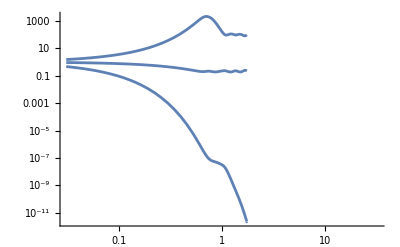

```mathematica
LogLogPlot[SingularValueList[JSol[t]],{t, 0, TMax}]
```

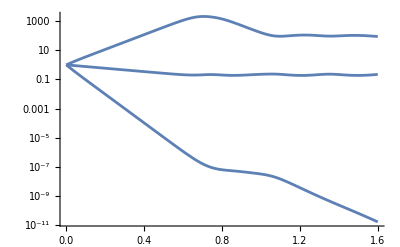

```mathematica
LogPlot[SingularValueList[JSol[t]],{t, 0, 0.05TMax}]
```